```mathematica
(* thermodynamics *)
```

```mathematica
e[m_,T_]=T^4/π^2(m/T)^2(3 BesselK[2,m/T]+m/T BesselK[1,m/T]);
p[m_,T_]=T^4/π^2(m/T)^2( BesselK[2,m/T]);
s[m_,T_]=(e[m,T]+p[m,T])/T//FullSimplify;
```

```mathematica
(* check speed of sound squared *)
```

```mathematica
cs2[m_,T_]=D[p[m,T],T]/D[e[m,T],T]//FullSimplify;
```

```mathematica
(* RR & AJ paper *)
```

```mathematica
cs2AJ[m_,T_]=(e[m,T]+p[m,T])/(3e[m,T]+(3+(m/T)^2)p[m,T])//FullSimplify;
```

```mathematica
cs2[m,T]-cs2AJ[m,T]//FullSimplify
```

0

```mathematica
(* RR & GD paper *)
```

```mathematica
I30[m_,T_]=T^5/π^2 z (z(z^2+12)BesselK[0,z]+(5 z^2+24)BesselK[1,z])/.z-> m/T;
```

```mathematica
cs2GD[m_,T_]=(e[m,T]+p[m,T])/(I30[m,T]/T)//FullSimplify;
```

```mathematica
cs2[m,T]-cs2GD[m,T]//FullSimplify;
```

```mathematica
(* trace anomaly *)
```

```mathematica
j[m_,T_]=p[m,T]-e[m,T]/3//FullSimplify;
```

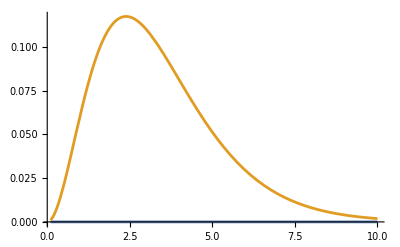

```mathematica
Plot[{0,j[z T ,T]/T^4(-3)},{z,0.1,10}]
```

```mathematica
(* shear and bulk viscosities -- RR & GD paper *)
```

```mathematica
Ki1[m_,T_]=π/2(1-z BesselK[0,z]StruveL[-1,z]-z BesselK[1,z]StruveL[0,z])/.z-> m/T//FullSimplify;
Im20[m_,T_]=1/π^2(BesselK[0,z]-z(BesselK[1,z] -  Ki1[m,T]))/.z-> m/T//FullSimplify;
ηGD[m_,T_]=4/5 p[m,T]+1/15(e[m,T]-3p[m,T])-m^4/15 Im20[m,T]//FullSimplify;
ζGD[m_,T_]=(1/3-cs2[m,T])(e[m,T]+p[m,T])-2/9(e[m,T]-3p[m,T])-m^4/9 Im20[m,T]//FullSimplify;
```

```mathematica
(* before solving EOMs, all variables are transformed to fermi using the rule: 1 fm/c = 5.0677 1/GeV *)
hbarc=0.1973269631;
```

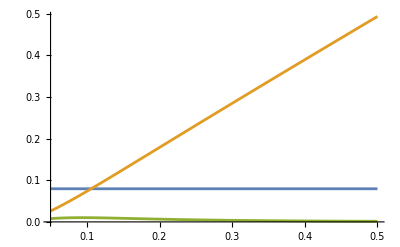

```mathematica
Plot[{1/(4π),ηGD[m,T]/(hbarc s[m,T])/.m->0.3 //FullSimplify,ζGD[m,T]/(hbarc s[m,T])/.m->0.3 //FullSimplify},{T,0.05,0.50}]
```

```mathematica
(* check scaling m -> 0 *)
```

```mathematica
Series[ζGD[m,T]/ηGD[m,T]/.m->z T //FullSimplify,{z,0,4}]
```

(25 z^4)/432+O[z]^5

```mathematica
Series[75(1/3-cs2[m,T])^2/.m->z T//FullSimplify,{z,0,4}]
```

(25 z^4)/432+O[z]^5

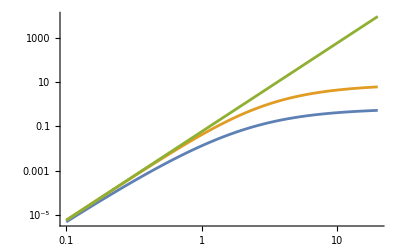

```mathematica
LogLogPlot[{ζGD[m,T]/ηGD[m,T]/.m->z T //FullSimplify,75(1/3-cs2[m,T])^2/.m->z T//FullSimplify,(25 z^4)/432},{z,0.1,20}]
```

```mathematica
(* solve for T[t], relaxation time = 1.0 fm assumed below *)
```

```mathematica
η=ηGD;
ζ=ζGD;
```

```mathematica
m=(0.300 (* GeV *))/hbarc;(* fm^-1 *)

(* initial and final values for time integration *)
ti=0.5; (* fm *)
tf=10.0;(* fm *)

(* initial value of temperature *)
Ti=(0.500 (* GeV *))/hbarc (* fm^-1 *)
```

2.53387

```mathematica
Tsol=NDSolve[{D[e[m,T[t]],t]+(e[m,T[t]]+p[m,T[t]])/t-1/t^2(4/3 η[m,T[t]]+ζ[m,T[t]])==0,T[ti]==Ti},T,{t,ti,tf}][[1,1,2]];
```

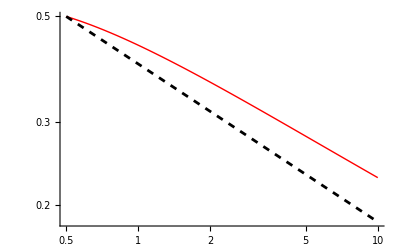

```mathematica
LogLogPlot[{Tsol[t]hbarc ,(Ti ti^(1/3))/t^(1/3)hbarc},{t,ti,tf},PlotStyle->{Directive[Red,Thick],Directive[Black,Dashed]}]
```

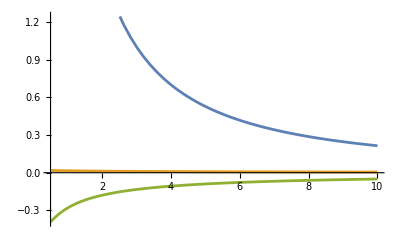

```mathematica
Plot[{η[m,T[t]]/.T-> Tsol,ζ[m,T[t]]/.T-> Tsol,j[m,T[t]]/.T-> Tsol},{t,ti,tf}]
```

```mathematica
(* initial value of our unknown field, should have dimension of (energy density)/T *)
```

```mathematica
Xi={1,0.3,-0.3,-1}
```

{1,0.3,-0.3,-1}

```mathematica
(* find initial T' from equation relating energy densities *)
```

```mathematica
Tpi=Table[FindRoot[e[m,Tp0]==e[m,Tsol[ti]]+Xi[[i]]/ti,{Tp0,Tsol[ti]}][[1,2]],{i,1,Length@Xi}]
```

{2.58371,2.54913,2.51832,2.48086}

```mathematica
dedT[M_,T_]=D[e[M,T],T]//FullSimplify;
```

```mathematica
(* below I solve for X[t], but since I do not know T'[t] I use a trick and solve this equation together with extra equation which comes from differentiation of the equation relating energy densities *)
```

```mathematica
Solution2=Table[NDSolve[{
dedT[m,Tp[t]]D[Tp[t],t]==dedT[m,Tsol[t]]D[Tsol[t],t]+D[X[t],t]/t-X[t]/t^2,
D[X[t],t]+X[t]/(3 t)+(j[m,Tp[t]]-j[m,Tsol[t]])==4/(3t)(η[m,Tp[t]]-η[m,Tsol[t]])+1/t(ζ[m,Tp[t]]-ζ[m,Tsol[t]]),X[ti]==Xi[[i]],Tp[ti]==Tpi[[i]]},{Tp,X},{t,ti,tf}] [[1]],{i,1,Length@Xi}];
Tpsol=Table[Solution2[[i,1,2]],{i,1,Length@Xi}];
Xsol=Table[Solution2[[i,2,2]],{i,1,Length@Xi}];
```

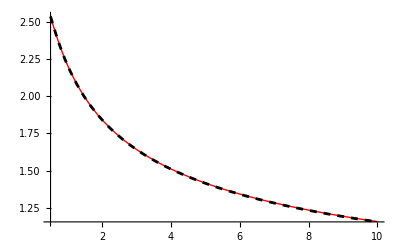

```mathematica
Plot[{Tsol[t],Tpsol[[1]][t] Tsol[ti]/(Tpsol[[1]][ti])},{t,ti,tf},PlotRange->All,PlotStyle->{Directive[Red,Thick],Directive[Black,Dashed]}]
```

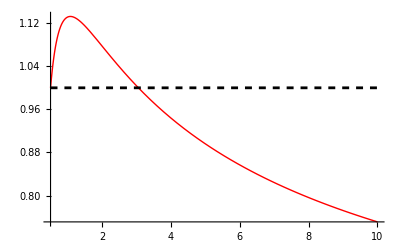

```mathematica
Plot[{Xsol[[1]][t],Xi[[1]]},{t,ti,tf},PlotRange->All,PlotStyle->{Directive[Red,Thick],Directive[Black,Dashed]}]
```

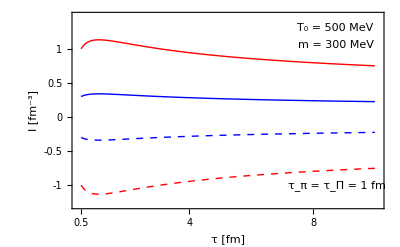

```mathematica
Plot[{Xsol[[1]][t],Xsol[[2]][t],Xsol[[3]][t],Xsol[[4]][t]},{t,ti,tf},PlotRange->{{0.4,10.1},{-1.29,1.48}},PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick,Dashed]},Frame->True,FrameLabel->{"τ [fm]","I [fm^-3]"},FrameStyle->Directive[Black,Thickness[0.005],14],FrameTicks->{{{{-1.2,""},{-1.1,""},{-1,"-1",0.03},{-0.9,""},{-0.8,""},{-0.7,""},{-0.6,""},{-0.5,"-0.5",0.03},{-0.4,""},{-0.3,""},{-0.2,""},{-0.1,""},{0,"0",0.03},{0.1,""},{0.2,""},{0.3,""},{0.4,""},{0.5,"0.5",0.03},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1,"1",0.03},{1.1,""},{1.2,""},{1.3,""},{1.4,""}},None},{{0.5,{1,"",0.015},{1.5,""},{2,"2",0.03},{2.5,""},{3,"",0.015},{3.5,""},{4,"4",0.03},{4.5,""},{5,"",0.015},{5.5,""},{6,"6",0.03},{6.5,""},{7,"",0.015},{7.5,""},{8,"8",0.03},{8.5,""},{9,"",0.015},{9.5,""},{10,"10",0.03}},None}},Epilog->{Text[Style["T_0 = 500 MeV"],{8.7,1.3}],Text[Style["m = 300 MeV"],{8.75,1.05}],Text[Style["τ_π = τ_Π = 1 fm"],{8.78,-1}]}]
```